CHAPTER ChapterLabel

Data Structures

Well I live with snakes and lizards 
And other things that go bump in the night

Ministry, “Everyday Is Halloween”

ChapterLabel.Heading1  Introduction

Higher mathematics is rich in structures and formalisms that take mathematics beyond the realm of numbers. This chapter includes a potpourri of recipes for data structures and algorithms that arise in linear algebra, tensor calculus, set theory, graph theory, and computer science. For the most part, lists form the foundation for these structures. Mathematica gains a lot of mileage by representing sets, vectors, matrices, and tensors using lists because all the generic list operations are available for their manipulation. Of course, a list, a set, and a tensor are very distinct entities from a mathematical point of view, but this distinction is handled by special- purpose functions rather than special-purpose data structures.

This introduction reviews the most common operations associated with list structures but is not an exhaustive reference. These operations will be used frequently throughout this book, so you should have some basic familiarity.

List Functions

The foundation of most data structures in Mathematica is the list. It is difficult to do much advanced work with Mathematica unless you are fluent in its functions for list processing. To this end, the initial recipes revolve around basic list processing. A list in Mathematica is constructed using the function List[elem1,elem2,...,elemN] or, more commonly, with curly brackets {elem1,elem2,...,elemN}. There is no restriction on the nature of these elements. They could be mixtures of numbers, strings, functions, other lists, or anything else Mathematica can represent (like graphic or sound data).

The first thing you need to know about lists is how to generate them. Table is the workhorse function for doing this. It has several variations that are most easily explained by example.

```mathematica
(*Ten copies of an expr; in this case, the constant 1*)
Table[1, {10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
(*The result of evaluation expr for i 1 to 10*)
Table[i^2, {i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
(*The result of evaluation expr for i 2 to 10*)
Table[i^2, {i,2,10}]
```

{4,9,16,25,36,49,64,81,100}

```mathematica
(*The result of evaluation expr for i 2 to 10 by steps of 2*)
Table[i, {i,2,10,2}]
```

{2,4,6,8,10}

```mathematica
(*2 x 3 matrix of constant 1*)
Table[1, {2},{3}]
```

{{1,1,1},{1,1,1}}

```mathematica
(*Tensor of rank three*)
Table[i+j^2+k^3, {i,0,2},{j,0,2},{k,0,2}]//MatrixForm
```

((0
1
8) | (1
2
9) | (4
5
12)
(1
2
9) | (2
3
10) | (5
6
13)
(2
3
10) | (3
4
11) | (6
7
14))

In addition to Table, Mathematica has several special-purpose list constructors: Range, Array, ConstantArray, DiagonalMatrix, and IdentityMatrix. These functions are less general than Table but are clearer and simpler to use when applicable. For example, consider IdentityMatrix and its Table equivalent.

```mathematica
IdentityMatrix[3]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*Equivalent to IdentityMatrix*)
Table[If[i==j,1,0],{i,1,3},{j,1,3}]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Sometimes using a special-purpose list constructor is more verbose. Consider these equivalent ways of generating an array of ten 1s. Here, 1& is the function that always returns 1.

```mathematica
Array[1&,10] == ConstantArray[1,10]
```

True

Once you have one or more lists, you can compose new lists using functions like Append, Prepend, Insert, Join, and Riffle.

```mathematica
list1 = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
list2 = list1 ^ 2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
(*Add elements to the end.*)
Append[list1, 11]
```

{1,2,3,4,5,6,7,8,9,10,11}

```mathematica
(*Add elements to the front.*)
Prepend[list1,0]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
(*Insert elements at specific positions.*)
Insert[list1, 3.5, 4]
```

{1,2,3,3.5,4,5,6,7,8,9,10}

```mathematica
(*Negative offsets to insert from the end*)
Insert[list1, 3.5, -4]
```

{1,2,3,4,5,6,7,3.5,8,9,10}

```mathematica
(*You can insert at multiple positions {{i1},{i2},...,{iN}}.*)
Insert[list1, 0, List /@ Range[2,Length[list1]]]
```

{1,0,2,0,3,0,4,0,5,0,6,0,7,0,8,0,9,0,10}

```mathematica
(*Join one or more lists.*)
Join[list1,list2]
```

{1,2,3,4,5,6,7,8,9,10,1,4,9,16,25,36,49,64,81,100}

```mathematica
(*Riffle is a function specifically designed to interleave elements.*)
Riffle[list1,0]
```

{1,0,2,0,3,0,4,0,5,0,6,0,7,0,8,0,9,0,10}

The flip side of building lists is taking them apart. Here you will use operations like Part, First, Last, Rest, Most, Take, Drop, Select, and Cases.

```mathematica
(*Part is frequently accessed via its operator [[expr]] equivalent.*)
 list1[[3]] == Part[list1,3]
```

True

```mathematica
(*Accessing the first element. Lisp programmers call this operation car.*)
First[list1]
```

1

```mathematica
(*Accessing the last element*)
Last[list1]
```

10

```mathematica
(*All but the first element. Lisp programmers call this operation cdr.*)
Rest[list1]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
(*All but the last element*)
Most[list1]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
(*The first three elements*)
Take[list1,3]
```

{1,2,3}

```mathematica
(*All but the first three*)
Drop[list1,3]
```

{4,5,6,7,8,9,10}

```mathematica
(*The elements in which some criterion is satisfied, in this case odd elements*)
Select[list1, OddQ]
```

{1,3,5,7,9}

```mathematica
(*The elements matching a pattern*)
Cases[list1 /3 ,a_Integer -> 3a]
```

{3,6,9}

See Chapter 5 for more information on patterns.

You rearrange and restructure lists using functions such as Reverse, RotateLeft, RotateRight, Flatten, Partition, Transpose, and Sort.

```mathematica
Reverse[list1]
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
RotateLeft[list1]
```

{2,3,4,5,6,7,8,9,10,1}

```mathematica
RotateRight[list1]
```

{10,1,2,3,4,5,6,7,8,9}

Partition and Flatten are very versatile functions for creating and removing structure. Flatten can be thought of as the inverse of Partition. Here, repeated partitioning using Nest converts a list to a binary tree.

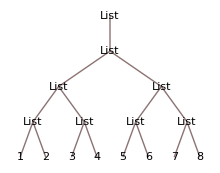

```mathematica
bifurcate[list_] := Nest[Partition[#,2]&,list,Floor[Log[2,Length[list]]]]
(structured = bifurcate[list1])//TreeForm
```

```mathematica
Flatten[structured]
```

{1,2,3,4,5,6,7,8}

Flatten can also take a level that tells it to flatten only up to that level.

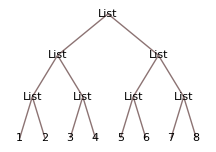

```mathematica
Flatten[structured,1]//TreeForm
```

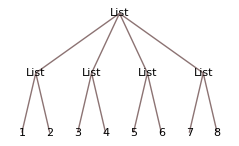

```mathematica
Flatten[structured,2]//TreeForm
```

```mathematica
Flatten[structured,3]
```

{1,2,3,4,5,6,7,8}

Many of these functions have advanced features, so you should refer to the Mathematica documentation for each to understand their full capabilities. I will use these functions frequently throughout this book without further explanation, so if you are not already familiar with them, you should take some time to experiment on your own.

Set Functions

A set in Mathematica is nothing more than a list that is normalized to eliminate duplicates upon application of a set operation: Union, Intersection, or Complement. To determine duplicates, Mathematica uses an option called SameTest, which by default is the function SameQ or ===. The function Subsets constructs a list of all subsets. MemberQ is used to test membership, but this function is far more general, and I will revisit it in Chapter 4.

```mathematica
Union[list1,list2]
```

{1,2,3,4,5,6,7,8,9,10,16,25,36,49,64,81,100}

```mathematica
Intersection[list1,list2]
```

{1,4,9}

```mathematica
(*Complement can be used with Intersection to implement Set Difference.*)
Complement[list1, Intersection[list1,list2]]
```

{2,3,5,6,7,8,10}

```mathematica
Complement[list2, Intersection[list1,list2]]
```

{16,25,36,49,64,81,100}

```mathematica
(*Generating all subsets*)
Subsets[{a,b,c}]
```

{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}}

```mathematica
MemberQ[list2,4]
```

True

Vector Functions

A vector is also represented by a list, but Mathematica has a special representation called a SparseArray that can conserve space when a vector contains many zero entries (see Recipe 3.8). Matrices and tensors are naturally represented as nested lists; these likewise can use SparseArrays.

Vector math is supported by the fact that most mathematical operations have the attribute Listable, meaning that the operations automatically thread over lists.

```mathematica
(*Multiplication and subtraction of a vector by a scalar*)
3 * list1 -3
```

{0,3,6,9,12,15,18,21,24,27}

```mathematica
(*Listable is the relevant property.*)
Intersection[Flatten[Attributes[{Times,Plus,Minus,Divide,Power}]]]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected,ReadProtected}

Same-sized vectors and matrices can also be added, multiplied, and so on, in an element-by-element fashion.

```mathematica
Range[10] ^ Range[10,1,-1]
```

{1,512,6561,16384,15625,7776,2401,512,81,10}

Vector-specific operations are also supported. Some of the more advanced operations are in a package called VectorAnalysis`, including CrossProduct, Norm, Div, Grad, Curl, and about three dozen others. Use ?VectorAnalysis`* after loading the package to see the full list.

```mathematica
u = {-1,0.5,1}; v = {1,-0.5,1};
```

```mathematica
u.v
```

-0.25

```mathematica
Norm[u]
```

1.5

```mathematica
Orthogonalize[{u,v}]
```

{{-0.666667,0.333333,0.666667},{0.596285,-0.298142,0.745356}}

```mathematica
Projection[u,v]
```

{-0.111111,0.0555556,-0.111111}

CrossProduct is not built in, so you must load a special package.

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
CrossProduct[u,v]
```

{1.,2.,0.}

Matrix and Tensor Functions

Vectors and matrices are familiar to most scientists, engineers, and software developers. A tensor is a generalization of vectors and matrices to higher dimensions. Specifically, a scalar is a zero-order tensor, a vector is a first-order tensor, and a matrix is a second-order tensor. Tensors of order three and higher are represented in Mathematica as more deeply nested lists. Here is an example of a tensor of order four. Note that the use of subscripting in this example is for illustration and is not integral to the notion of a tensor from Mathematica’s point of view. (Mathematicians familiar with tensor analysis know that subscripts and superscripts have very definite meaning, but Mathematica does not directly support those notations [although some third-party packages do].)

```mathematica
(tensor4 = Table[Subscript[a,i,j,k,l], {i,1,2}, {j,1,2},{k, 1,2}, {l, 1,2}])//MatrixForm
```

((a_(1,1,1,1) | a_(1,1,1,2)
a_(1,1,2,1) | a_(1,1,2,2)) | (a_(1,2,1,1) | a_(1,2,1,2)
a_(1,2,2,1) | a_(1,2,2,2))
(a_(2,1,1,1) | a_(2,1,1,2)
a_(2,1,2,1) | a_(2,1,2,2)) | (a_(2,2,1,1) | a_(2,2,1,2)
a_(2,2,2,1) | a_(2,2,2,2)))

```mathematica
(*Using Part with a single index yields a third-order tensor.*)
tensor4[[1]]//MatrixForm
```

((a_(1,1,1,1)
a_(1,1,1,2)) | (a_(1,1,2,1)
a_(1,1,2,2))
(a_(1,2,1,1)
a_(1,2,1,2)) | (a_(1,2,2,1)
a_(1,2,2,2)))

```mathematica
(*Using Part with two indices on a fourth-order tensor yields a second-order tensor (i.e., a matrix).*)
tensor4[[1,1]]//MatrixForm
```

(a_(1,1,1,1) | a_(1,1,1,2)
a_(1,1,2,1) | a_(1,1,2,2))

```mathematica
(*Using Part with three indices yields a vector.*)
tensor4[[1,1,2]]
```

{a_(1,1,2,1),a_(1,1,2,2)}

```mathematica
(*And all 4 indices gives a scalar.*)
tensor4[[2,1,2,2]]
```

a_(2,1,2,2)

The recipes in this chapter deal mostly with vectors and matrices, but many operations in Mathematica are generalized to higher-order tensors. A very important function central to linear algebra is the Dot product. In linear algebra texts, this is often referred to simply as vector multiplication. The Dot product only works if vectors and matrices have compatible shapes.

```mathematica
Dot[{x1,x2,x3},{y1,y2,y3}]
```

x1 y1+x2 y2+x3 y3

```mathematica
Clear[x,y];
Dot[Table[Subscript[x,i,j], {i,1,3}, {j,1,2}], Table[Subscript[y,i,j], {i,1,2}, {j,1,3}]]//MatrixForm
```

(x_(1,1) y_(1,1)+x_(1,2) y_(2,1) | x_(1,1) y_(1,2)+x_(1,2) y_(2,2) | x_(1,1) y_(1,3)+x_(1,2) y_(2,3)
x_(2,1) y_(1,1)+x_(2,2) y_(2,1) | x_(2,1) y_(1,2)+x_(2,2) y_(2,2) | x_(2,1) y_(1,3)+x_(2,2) y_(2,3)
x_(3,1) y_(1,1)+x_(3,2) y_(2,1) | x_(3,1) y_(1,2)+x_(3,2) y_(2,2) | x_(3,1) y_(1,3)+x_(3,2) y_(2,3))

Inner[f,m1,m2,g] is a function that generalizes Dot by allowing a function f to take the place of multiplication and g to take the place of addition. Here are some examples.

```mathematica
Inner[List,Table[i^j, {i,1,4}, {j,1,3}], Table[j!  i!, {i,1,3}, {j,1,4}],Max]//MatrixForm
```

(6 | 12 | 36 | 144
8 | 12 | 36 | 144
27 | 27 | 36 | 144
64 | 64 | 64 | 144)

```mathematica
Inner[List,Table[i+j, {i,1,3}, {j,1,2}], Table[i*j, {i,1,2}, {j,1,3}],List]//MatrixForm
```

((2 | 1
3 | 2) | (2 | 2
3 | 4) | (2 | 3
3 | 6)
(3 | 1
4 | 2) | (3 | 2
4 | 4) | (3 | 3
4 | 6)
(4 | 1
5 | 2) | (4 | 2
5 | 4) | (4 | 3
5 | 6))

```mathematica
Inner[List,Table[i*j, {i,1,2}, {j,1,2}], Table[i+j, {i,1,2}, {j,1,2}],Join]//MatrixForm
```

((1
2
2
3) | (1
3
2
4)
(2
2
4
3) | (2
3
4
4))

```mathematica
Inner[And,Table[i < j, {i,1,3}, {j,1,3}], Table[j< i, {i,1,3}, {j,1,3}],Or]//MatrixForm
```

(True | True | False
True | True | False
False | False | False)

ChapterLabel.Heading1  Ensuring the Most Efficient Representation of Numerical Lists

Problem

You are performing very mathematically intense computations on large vectors, matrices, or higher-order tensors and want the most efficient representation in terms of speed and space.

Solution

Make sure your lists are packed arrays by not mixing numerical types. This means arrays of integers should work exclusively in integers or exclusively in machine precision floating point. Use of uniform types is necessary but not sufficient for getting packed arrays. Mathematica tries to automatically use packed arrays when generating large lists of numbers, but sometimes subtle coding differences prevent it from packing the result.

Here are two very similar pieces of code, but the first generates an unpacked representation and the second generates a packed one.

```mathematica
array1= N[Table[i * Pi, {i,0,500000}]];
Developer`PackedArrayQ[array1]
```

False

```mathematica
array2= Table[i * Pi, {i,0.0,500000.0}];
Developer`PackedArrayQ[array2]
```

True

The difference is that the first Table generates a table in symbolic form and then converts it to real numbers with N. So, although the final array meets the uniform criteria, N will not pack it. In the second version, I force Table to create a list of real numbers right off the bat by using real bounds for the index i. This makes N unnecessary and causes Table to return a packed result.

Discussion

To get some insight into the superiority of packed arrays, we can ask Mathematica to tell us the size of each array from the solution.

```mathematica
Grid[{{"","size","per elem"},
{"array1",ByteCount[array1],N[ByteCount[array1]/Length[array1]]}, 
{"array2",ByteCount[array2],N[ByteCount[array2]/Length[array2]]}},
Alignment->Right,Frame->All]
```

| size | per elem
array1 | 12000056 | 24.0001
array2 | 4000132 | 8.00025

As you can see, the space saved is considerable. Essentially, packed is giving you the equivalent of a C or Fortran array. Space savings is not the only reason to work with packed arrays. Many operations are considerably faster as well. Here you see that multiplication of packed arrays is an order of magnitude faster than unpacked!

```mathematica
Mean@Table[Timing[array1*array2][[1]],{100}]
```

0.0909364

```mathematica
Mean@Table[Timing[array2*array2][[1]],{100}]
```

0.00625822

When you can get an order of magnitude improvement, it is a good idea to take it, because life is short!

The Developer` package has a function to pack an unpacked array, although it is preferable to alter your coding style as we’ve discussed here to get packed arrays.

```mathematica
array1=Developer`ToPackedArray[array1];
Developer`PackedArrayQ[array1]
```

True

If you have a very large packed array and assign a value to one of the elements that differ from the packed type, this assignment will be expensive relative to a normal assignment. Mathematica will be forced to copy the entire array into unpacked form before the assignment can be made.

See Also

The Developer` package also has a function Developer`FromPackedArray for converting a packed form back to the normal representation. Evaluating ?"Developer`*" allows you to peruse all the functions in this package, but many are undocumented.

ChapterLabel.Heading1  Sorting Lists

Problem

You need to sort a list based on standard ordering (Less) or a custom-ordering relation. One common reason for sorting is to enable binary search.

Solution

Use Sort or SortBy, depending on how the ordering relation is specified. By default, Sort uses less than (<) to order elements.

```mathematica
list = RandomInteger[{-100,100},10];
```

```mathematica
Sort[list]
```

{-73,-50,-45,-43,-20,2,42,50,66,84}

```mathematica
Sort[list,Greater]
```

{84,66,50,42,2,-20,-43,-45,-50,-73}

SortBy does not use an ordering relation, but rather uses a function whose output is passed to Less.

```mathematica
SortBy[list, Abs]
```

{2,-20,42,-43,-45,-50,50,66,-73,84}

Discussion

If you need to sort lists containing objects more complicated than scalars, you will need to be comfortable with expressing the order relation function. Here are some examples.

```mathematica
data = {
{"21 Mar 2007 14:34:30",10.1,12.7,13.3},
{"21 Jun 2005 10:19:30",10.3,11.7,11.7},
{"21 Aug 2006 15:34:01",11.7,16.8,8.6},
{"21 Aug 2006 09:34:00",11.9,16.5,8.6}
};
(*Sort the data by the time entry, which must be converted to an absolute time to be properly ordered.*)
Sort[data,Less[AbsoluteTime[{#1[[1]],{"Day","MonthNameShort","Year","Time"}}],AbsoluteTime[{#2[[1]],{"Day","MonthNameShort","Year","Time"}}]]&]//TableForm
```

21 Jun 2005 10:19:30 | 10.3 | 11.7 | 11.7
21 Aug 2006 09:34:00 | 11.9 | 16.5 | 8.6
21 Aug 2006 15:34:01 | 11.7 | 16.8 | 8.6
21 Mar 2007 14:34:30 | 10.1 | 12.7 | 13.3

For practical sorting, you will never need to look beyond Sort, because it is both fast and flexible. However, if you are interested in sorting from an algorithmic perspective, Mathematica also has a package called Combinatorica`, which contains some sorting routines that use specific algorithms (SelectionSort, HeapSort).

```mathematica
Needs["Combinatorica`"]
```

```mathematica
SelectionSort[list,Less]
```

{-73,-50,-45,-43,-20,2,42,50,66,84}

Of course, there is probably no practical reason to use SelectionSort since its asymptotic behavior is O(n^2), whereas Sort uses a O(n log n) algorithm. You can count the number of comparisons each sort makes using a custom comparison function. The framed number is the comparison count.

```mathematica
(*The sorted list and count of comparisons with Sort*)Block[{count = 0},{Sort[list,(count++;Less[#1,#2])&],Framed[count]}]
```

{{-73,-50,-45,-43,-20,2,42,50,66,84},26}

```mathematica
(*Comparisons consistent with n log n*)
Log[2.0,Length[list]] * Length[list]
```

33.2193

```mathematica
(*The sorted list and count of comparisons with SelectionSort. Roughly twice the comparisons*)
Block[{count = 0},{SelectionSort[list,(count++;Less[#1,#2])&],Framed[count]}]
```

{{-73,-50,-45,-43,-20,2,42,50,66,84},55}

```mathematica
(*Although better than worst case*)
Length[list]^2
```

100

Heap sort is O(n log n), but the Combinatorica` implementation is somewhat  crippled because the ordering operation cannot be customized.

```mathematica
HeapSort[list]
```

{-73,-50,-45,-43,-20,2,42,50,66,84}

If you are keen to do this experiment with HeapSort, you can easily make a customi-zable version, since the source code is available.

```mathematica
genericHeapSort[{},_]:={}
genericHeapSort[p_List,ordering_]:=Module[{heap=genericHeapify[p,ordering],min},Append[Table[min=First[heap];heap[[1]]=heap[[n]];heap=genericHeapify[Drop[heap,-1],1,ordering];min,{n,Length[p],2,-1}],Max[heap]]]/;Length[p]>0
(*HeapSort is implemented in terms of a function Heapify,  which we must customize to inject our ordering.*)
genericHeapify[p_List,ordering_]:=Module[{j,heap=p},Do[heap=genericHeapify[heap,j,ordering],{j,Quotient[Length[p],2],1,-1}];heap]
genericHeapify[p_List,k_Integer,ordering_]:=Module[{hp=p,i=k,l,n=Length[p]},While[(l=2 i)≤n,If[l<n&&ordering[hp[[l+1]],hp[[l]]],l++];If[ordering[hp[[l]],hp[[i]]],{hp[[i]],hp[[l]]}={hp[[l]],hp[[i]]};i=l,i=n+1];];hp]
```

```mathematica
Block[{count = 0},{genericHeapSort[list,(count++;Less[#1,#2])&],Framed[count]}]
```

{{-73,-50,-45,-43,-20,2,42,50,66,84},39}

It is unfortunate that we have to hack HeapSort to give it customizable ordering function. When you develop your own general-purpose functions, it pays to consider facilities that allow you and other users to customize the details while leaving the essential algorithm intact. This is the essence of what is called generic programming. Chapter 2 has several recipes that demonstrate how to create more generic functions.

One application of sorting is performing efficient search. The Combinatorica` package provides the function BinarySearch, which requires a sorted list. BinarySearch returns the index of the first occurrence of a search key, if found. If the key is not found, it returns index + 1/2, indicating that the key belongs between index and index + 1 if it were to be inserted.

```mathematica
list2 = Range[1,20,2]
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
BinarySearch[list2, 7]
```

4

```mathematica
BinarySearch[list2, 6]
```

7/2

```mathematica
(*An example of how BinarySearch might be used to conditionally insert new elements into a sorted list*)
value = 6 ;
pos = BinarySearch[list2, value];
If[IntegerQ[pos],pos,pos=Ceiling[pos];list2=Insert[list2,value,pos];pos];
list2
```

{1,3,5,6,7,9,11,13,15,17,19}

See Also

Recipe 3.3 discusses how to determine sorted order without rearranging the elements of the list.

A good overview of various sorting algorithms can be found at http://bit.ly/2bRckv.

ChapterLabel.Heading1  Determining Order Without Sorting

Problem

You need to know how the elements of a list are ordered without actually sorting them. This may be because it is too expensive to keep multiple copies of the data in various orderings.

Solution

Use Ordering to get a list of offsets to the elements in the order they would appear if sorted.

```mathematica
unsorted = RandomInteger[{90,99},10]
```

{98,90,91,98,98,91,99,99,97,96}

```mathematica
Ordering[unsorted]
```

{2,3,6,10,9,1,4,5,7,8}

Discussion

Ordering has two variations. The first takes an integer that limits how many positions are returned. If you specify n, then the first n are returned; if you specify -n, the last n are returned. This option makes Ordering more useful than Sort when you don’t need the entire list sorted.

```mathematica
Ordering[unsorted,3]
```

{2,3,6}

```mathematica
Ordering[unsorted,-3]
```

{5,7,8}

The second variation takes both an integer and an ordering relation.

```mathematica
Ordering[unsorted, Length[unsorted], Greater]
```

{8,7,5,4,1,9,10,6,3,2}

Given an ordering, it is easy to create a sorted version of the list.

```mathematica
unsorted[[Ordering[unsorted]]]
```

{90,91,91,96,97,98,98,98,99,99}

Unfortunately, Ordering does as many comparisons as a full sort even if you only want the first few orderings.

```mathematica
Block[{count = 0},{Ordering[unsorted,3,(count++;Less[#1,#2])&],Framed[count]}]
```

{{2,6,3},23}

```mathematica
Block[{count = 0},{Ordering[unsorted,6,(count++;Less[#1,#2])&],Framed[count]}]
```

{{2,6,3,10,9,5},23}

A heap would be superior in such an application, but rolling your version of Ordering is unlikely to yield superior results due to optimizations that go beyond minimizing comparisons. After all, it takes Ordering less than a second to do its work on a million integers on my relatively low-powered laptop.

```mathematica
Timing[Ordering[RandomInteger[{1, 999999}, 1000000],2]]
```

{0.255152,{314075,337366}}

See Also

Recipe 3.2 discusses sorting.

OrderedQ tests if a list is ordered, and Order compares two expressions, returning –1 (Less), 0 (Equal), or 1 (Greater).

ChapterLabel.Heading1  Extracting the Diagonals of a Matrix

Problem

You want to extract the diagonal, subdiagonal, superdiagonal, or antidiagonal of a matrix.

Solution

In versions prior to Mathematica 6, use Tr with List as the combining function (the default combining function of Tr is Plus).

```mathematica
(matrix = {{1,2,3},{4,5,6}, {7,8,9}})//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
Tr[matrix,List]
```

{1,5,9}

Mathematica 6 introduced the function Diagonal, which makes this recipe trivial.

```mathematica
Diagonal[matrix]
```

{1,5,9}

You can extract the antidiagonal using either of the following expressions:

```mathematica
Diagonal[Map[Reverse,matrix]]
```

{3,5,7}

```mathematica
Tr[Map[Reverse,matrix],List]
```

{3,5,7}

Discussion

The Diagonal function is more versatile than Tr in that it allows you to select off the main diagonal by proving an index.

```mathematica
Diagonal[matrix,1]
```

{2,6}

```mathematica
Diagonal[matrix, -1]
```

{4,8}

Although the solutions implementation of antidiagonal is simple, it is not the most efficient: it reverses every row of the input matrix. An iterative solution using Table is simple and fast.

```mathematica
AntiDiagonal[matrix_] := Module[{len=Length[matrix]},
Table[matrix[[i,len-i+1]],{i,1,len}]]
```

```mathematica
bigMatrix = Table[i*j,{i,0,5500},{j,0,5500}];
```

```mathematica
Timing[AntiDiagonal[bigMatrix]][[1]]
```

0.001839

```mathematica
Timing[Diagonal[Map[Reverse, bigMatrix]]][[1]]
```

0.230145

It is always good to test a new version of an algorithm against one you already know works.

```mathematica
AntiDiagonal[bigMatrix] == Diagonal[Map[Reverse, bigMatrix]]
```

True

ChapterLabel.Heading1  Constructing Matrices of Specific Structure

Problem

You want to construct matrices of a specific structure (e.g., diagonal, identity, tridiagonal).

Solution

Mathematica has built-in matrix constructions for the most common kinds of matrices.

```mathematica
IdentityMatrix[5]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
DiagonalMatrix[Range[4]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 3 | 0
0 | 0 | 0 | 4)

Discussion

Although identity and diagonal matrices are quite common, there are other kinds of matrices that arise frequently in practical problems. For example, problems involving coupled systems often give rise to tridiagonal matrices. SparseArray and Band are perfect for this job. These are discussed in Recipe 3.8. Here, the use of Normal to convert sparse form to list form is not essential because sparse arrays will play nicely with regular ones.

```mathematica
triDiagonal[sub_List, main_List, super_List] /; {Length[sub],Length[super]}+1 == {Length[main] , Length[main]} :=
Module[{},
Normal[SparseArray[{Band[{2,1}]->sub,Band[{1,2}]->super,Band[{1,1}]->main},Length[main]]]]
```

```mathematica
triDiagonal[sub_?NumericQ,main_?NumericQ,super_?NumericQ,n_Integer] :=
Normal[SparseArray[{Band[{2,1}]->sub,Band[{1,2}]->super,Band[{1,1}]->main},n]]
```

```mathematica
triDiagonal[{-1,-1,-1},{2,2,2,2},{1,1,1}]//MatrixForm
```

(2 | 1 | 0 | 0
-1 | 2 | 1 | 0
0 | -1 | 2 | 1
0 | 0 | -1 | 2)

Tridiagonal matrices are always invertible.

```mathematica
Inverse[triDiagonal[{-1,-1,-1},{2,2,2,2},{1,1,1}]]
```

{{12/29,-5/29,2/29,-1/29},{5/29,10/29,-4/29,2/29},{2/29,4/29,10/29,-5/29},{1/29,2/29,5/29,12/29}}

There are also functions to transform a given matrix to another. Mathematica 7 in-troduced LowerTriangularize and UpperTriangularize to create triangular matrices from a given matrix.

```mathematica
With[{m=Array[1&,{4,4}]},Row[{LowerTriangularize[m] //MatrixForm,UpperTriangularize[m]//MatrixForm}]]
```

(1 | 0 | 0 | 0
1 | 1 | 0 | 0
1 | 1 | 1 | 0
1 | 1 | 1 | 1)(1 | 1 | 1 | 1
0 | 1 | 1 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1)

These functions take an optional second parameter k, where positive k refers to subdiagonals above the main diagonal and negative k refers to subdiagonals below the main diagonal. This points to another way to arrive at a tridiagonal matrix from a given or synthesized matrix.

```mathematica
UpperTriangularize[LowerTriangularize[Array[#&,{4,4}],1],-1]//MatrixForm
```

(1 | 1 | 0 | 0
2 | 2 | 2 | 0
0 | 3 | 3 | 3
0 | 0 | 4 | 4)

See Also

Certain important transformation matrices are accommodated by ScalingMatrix, RotationMatrix, and ReflectionMatrix. See Recipe 2.11 for a usage example.

ChapterLabel.Heading1  Constructing Permutation and Shift Matrices

Problem

You want to construct a matrix that will permute or shift the rows or columns of an input matrix.

Solution

A permutation matrix is a permutation of the identity matrix. It is used to permute either the rows or columns of another matrix.

```mathematica
permutationMatrix[list_] := IdentityMatrix[Length[list]][[list]]
```

```mathematica
(m1 = Table[2i +j, {i,1,3}, {j,1,3}])//MatrixForm
```

(3 | 4 | 5
5 | 6 | 7
7 | 8 | 9)

```mathematica
(*Create a permutation matrix that permutes the second and first row or column.*)
(p1 = permutationMatrix[{2,1,3}])//MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

```mathematica
(m1p1 = Dot[m1,p1])//MatrixForm (*Permute columns.*)
```

(4 | 3 | 5
6 | 5 | 7
8 | 7 | 9)

```mathematica
(p1m1 =Dot[p1,m1])//MatrixForm (*Permute rows.*)
```

(5 | 6 | 7
3 | 4 | 5
7 | 8 | 9)

Whereas a permutation matrix permutes rows or columns, a shift matrix shifts rows or columns, replacing the empty elements with zeros. A shift matrix is simply a matrix with 1s on the superdiagonal or subdiagonal and 0s everywhere else. This can easily be constructed using the DiagonalMatrix function.

```mathematica
shiftMatrix[n_,dir_] := DiagonalMatrix[Table[1,{n-Abs[dir]}],dir]
```

```mathematica
Dot[shiftMatrix[4,2],Table[1,{i,1,4},{j,1,4}]]//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(*Shift columns right.*)
Dot[m1, shiftMatrix[3,1]]//MatrixForm
```

(0 | 3 | 4
0 | 5 | 6
0 | 7 | 8)

```mathematica
(*Shift columns left.*)
Dot[m1, shiftMatrix[3,-1]]//MatrixForm
```

(4 | 5 | 0
6 | 7 | 0
8 | 9 | 0)

```mathematica
(*Shift rows up.*)
Dot[ shiftMatrix[3, 1],m1] // MatrixForm
```

(5 | 6 | 7
7 | 8 | 9
0 | 0 | 0)

```mathematica
(*Shift rows down.*)
Dot[ shiftMatrix[3, -1], m1] // MatrixForm
```

(0 | 0 | 0
3 | 4 | 5
5 | 6 | 7)

Discussion

A generalized permutation matrix has the same zero entries as the corresponding  permutation matrix, but the nonzero entries can have values other than 1.

```mathematica
generalizedPermutationMatrix[values_List, perm_List] := Dot[DiagonalMatrix[values], permutationMatrix[perm]]
```

```mathematica
generalizedPermutationMatrix[{3,-1,4}, {2,3,1}]//MatrixForm
```

(0 | 3 | 0
0 | 0 | -1
4 | 0 | 0)

You can easily enumerate all n! permutation matrices of size n.

```mathematica
allPermutationMatrices[n_] := permutationMatrix[#]& /@ Permutations[Range[n]]
```

```mathematica
Grid[Partition[MatrixForm /@ allPermutationMatrices[4],6]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0) | (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0) | (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0) | (0 | 1 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 0) | (0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0)
(0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1) | (0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1) | (0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 0)
(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0) | (0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0) | (0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

It is also easy to detect if a matrix is a row permutation of another matrix: simply remove each row from m1 that matches m2 and see if you are left with no rows. Of course, you must also check that the matrices are the same size. A check for column permutation is just a check for row permutations on the transpose of each matrix.

```mathematica
isRowPermutation[m1_,m2_] := Length[m1] == Length[m2] && Fold[DeleteCases[#1,#2]&,m1,m2] == {}
isMatrixPermutation[m1_,m2_] := isRowPermutation[m1,m2] || isRowPermutation[Transpose[m1],Transpose[m2]]
```

You can verify this on some test cases.

```mathematica
(*Obviously a matrix is a permutation of itself.*)
isMatrixPermutation[m1,m1]
```

True

```mathematica
(*Test a row permutation.*)
isMatrixPermutation[m1, p1m1]
```

True

```mathematica
(*Test a column permutation.*)
isMatrixPermutation[m1, m1p1]
```

True

```mathematica
(*A matrix and its tranpose are not permutations unless symmetric.*)
isMatrixPermutation[m1,Transpose[m1]]
```

False

You may be thinking that matrix permutations via linear algebra will only apply to matrices of numbers, but recall that Mathematica is a symbolic language and, thus, not limited to numerical manipulation. Here we do a Dot product on a matrix of graphics!

```mathematica
greenRook = Import[FileNameJoin[{NotebookDirectory[],"..","images","greenRook.gif"}]];
redSq = Import[FileNameJoin[{NotebookDirectory[],"..","images","redSq.gif"}]];
greenSq = Import[FileNameJoin[{NotebookDirectory[],"..","images","greenSq.gif"}]];
piece[i_,j_] := Which[i == j,greenRook,OddQ[i+j], redSq,True,greenSq];
(board = Table[piece[i,j], {i,1,4},{j,1,4}])//MatrixForm
```

(-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-)

```mathematica
Dot[board, permutationMatrix[{2, 3, 1, 4}]] // MatrixForm
```

(-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-)

This chess demo lacks some aesthetics (the squares move along with the rooks), but it does illustrate the generality of the permutation matrix.

ChapterLabel.Heading1  Manipulating Rows and Columns of Matrices

Problem

You want to add, remove, or modify entire rows or columns of a matrix in place.

Solution

Many operations on lists (including higher-order lists such as matrices) do not modify the input list but rather produce a new list with the change. For example, Append[myList,10] returns a list with 10 appended but leaves myList untouched. Sometimes you want to modify the actual value of the list associated with a symbol.

```mathematica
(*Create a 5 x 5 zero matrix.*)
(x = Table[0, {5},{5}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
(*Set the second column to {1,2,3,4,5}.*)
x[[All,2]] = Range[5];
```

```mathematica
x//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0)

```mathematica
(*Set the third row to 3.*)
x[[3,All]] = 3;
```

```mathematica
x//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
3 | 3 | 3 | 3 | 3
0 | 4 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0)

```mathematica
(*Set 3 x 3 interior to 9.*)
x[[2;;4,2;;4]] = 9;
```

```mathematica
x//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 9 | 9 | 9 | 0
3 | 9 | 9 | 9 | 3
0 | 9 | 9 | 9 | 0
0 | 5 | 0 | 0 | 0)

You may also want to add elements, rows, and columns.

```mathematica
(*Add a row.*)
AppendTo[x,Range[10,14]];
```

```mathematica
x//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 9 | 9 | 9 | 0
3 | 9 | 9 | 9 | 3
0 | 9 | 9 | 9 | 0
0 | 5 | 0 | 0 | 0
10 | 11 | 12 | 13 | 14)

```mathematica
(*Add a column of 9s.*)
Do[AppendTo[x[[i]],9],{i,1,6}]
```

```mathematica
x//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 9
0 | 9 | 9 | 9 | 0 | 9
3 | 9 | 9 | 9 | 3 | 9
0 | 9 | 9 | 9 | 0 | 9
0 | 5 | 0 | 0 | 0 | 9
10 | 11 | 12 | 13 | 14 | 9)

Discussion

Destructive operations should generally be avoided because they can lead to annoying bugs. For one thing, they make code sensitive to evaluation order. This type of code is harder to change. Further, you need to keep in mind that these operations are being performed on symbols rather than lists. What does this mean? Let’s inspect the attributes of AppendTo to gain a bit of insight.

```mathematica
Attributes[AppendTo]
```

{HoldFirst,Protected}

The relevant attribute here is HoldFirst. This means that the expression passed as the first argument is passed in unevaluated form. This has implications when you want to write your own functions that destructively change the value of a symbol. Consider trying to implement your own AppendTo.

```mathematica
ClearAll[myAppendTo] ;
myAppendTo[x_, val_] := x = Append[x, val]
```

```mathematica
Attributes[myAppendTo]
```

{}

```mathematica
x = {} ; myAppendTo[x, 10]
```

Set::shape: Lists {} and {10} are not the same shape.

{10}

```mathematica
x
```

{}

First notice that this generated an error message and that x did not change. This occurred because x was evaluated before the call, and you ended up evaluating AppendTo[List[], 10], which is illegal. You can remedy this by using HoldFirst.

```mathematica
SetAttributes[myAppendTo, {HoldFirst}]
```

```mathematica
myAppendTo[x,10]
```

{10}

```mathematica
x
```

{10}

Now it works. As a general rule, you need to use attributes HoldFirst, HoldRest, or HoldAll, as appropriate, to pass expressions in unevaluated form to your own functions. This is covered in Chapter 2, “Introduction,” on page 30, and in Recipe 2.2.

ChapterLabel.Heading1  Using Sparse Arrays to Conserve Memory

Problem

You need to work with very large arrays or matrices but most of the entries are duplicates (typically 0).

Solution

Mathematica has direct support for sparse arrays and higher-order tensors using the SparseArray function. The sparse array is built from a rule-based specification that maps positions to values.

```mathematica
(*1000 × 1000 sparse matrix*)
m1 = SparseArray[{{1,1}->1, {1000,1000}->-1, {500,750} -> 5}]
```

SparseArray[<3>,{1000,1000}]

You can also specify the positions and values in separate lists. Here is a sparse vector using this technique.

```mathematica
v1 = SparseArray[{1,3,9,81,6561} -> {5,10,15,20,25}]
```

SparseArray[<5>,{6561}]

You can also convert a standard matrix to a sparse one.

```mathematica
dense = DiagonalMatrix[Range[1000]];
```

```mathematica
sparse = SparseArray[dense]
```

SparseArray[<1000>,{1000,1000}]

As you can see, the memory savings is considerable.

```mathematica
ByteCount[dense] - ByteCount[sparse]
```

3987416

```mathematica
ClearAll[dense]
```

Discussion

Very large but sparsely populated matrices arise often in applications of linear algebra. Mathematica provides excellent support for sparse arrays because most operations that are available for list-based matrices (or tensors in general) are available for sparse array objects.

Mathematica does not have sparse equivalents of the convenience functions IdentityMatrix and DiagonalMatrix, but they are easy to synthesize using Band, which specifies either the starting position of a diagonal entry or a range of positions for a diagonal.

```mathematica
(*100 x 100 identity matrix*)
identity = SparseArray[Band[{1,1}] -> 1, {100,100}]
```

SparseArray[<100>,{100,100}]

```mathematica
(*100 x 100 diagonal matrix with the values {1,2,3,...,100} on the diagonal*)diagonal = SparseArray[Band[{1,1}] -> Range[100], {100,100}]
```

SparseArray[<100>,{100,100}]

A general sparse diagonal function looks like this.

```mathematica
sparseDiagonal[list_,k_] := SparseArray[Band[If[k>0,{1,1+k},{1-k,1}]]->list,(Length[list]+Abs[k]){1,1}]
```

You can also produce sparse versions of the permutation matrices from Recipe 3.6.

```mathematica
sparsePermutationMatrix[list_] := SparseArray[Band[{1,1}] -> 1, Length[list]{1,1}] [[list]]
antiDiag = sparsePermutationMatrix[Range[100,1,-1]]
```

SparseArray[<100>,{100,100}]

See Also

Recipe 3.5 showed how to use SparseArray and Band to create tridiagonal matrices.

ChapterLabel.Heading1  Manipulating Deeply Nested Lists Using Functions with Level Specifications

Problem

You need to extract, delete, modify, or transform content deep inside a nested list.

Solution

A level specification (or levelspec) is the key for surgically manipulating lists that contain many levels. Most of Mathematica’s functions that deal with lists have variations that take levelspecs. Position is one such function. Consider a list of integers that has values nested up to eight levels.

```mathematica
deep = {1,{2,3,4,5,{1,6,1,7},{1,{{{{1,8},1},{1}},1}},1,1,1,9,10,11},12};
Depth[deep]
```

8

```mathematica
deep//TreeForm
```

-Graphics-

If you use Position to search for 1, you get a list of all positions that have the value 1. You can verify this using Extract.

```mathematica
Position[deep,1]
```

{{1},{2,5,1},{2,5,3},{2,6,1},{2,6,2,1,1,1,1},{2,6,2,1,1,2},{2,6,2,1,2,1},{2,6,2,2},{2,7},{2,8},{2,9}}

```mathematica
Extract[deep,Position[deep,1]]
```

{1,1,1,1,1,1,1,1,1,1,1}

Suppose you do not want the 1s at every level. This is where levelspecs come in handy.

Use a single positive integer n to search at all levels up to and including n.

```mathematica
(*Only search up to level two.*)
Position[deep,1,2]
```

{{1},{2,7},{2,8},{2,9}}

Enclosing the level {n} in a list restricts search to that level.

```mathematica
(*Only search at level two.*)
Position[deep,1,{2}]
```

{{2,7},{2,8},{2,9}}

The list notation {n,m} restricts search to levels n through m, inclusively.

```mathematica
(*Search at levels three through five.*)
Position[deep,1,{3,5}]
```

{{2,5,1},{2,5,3},{2,6,1},{2,6,2,2}}

Negative level specification of the form -n looks for objects that themselves have depth n.

```mathematica
Position[deep,1,-1]
```

{{1},{2,5,1},{2,5,3},{2,6,1},{2,6,2,1,1,1,1},{2,6,2,1,1,2},{2,6,2,1,2,1},{2,6,2,2},{2,7},{2,8},{2,9}}

```mathematica
(*See the discussion for why this is empty and must be empty.*)
Position[deep,1,-2]
```

{}

Discussion

We used Position to get a feel for level specifications because it is easy to judge, based on the length of each position sublist, the depth of each item found. However, you may be surprised that the last example was empty. It is easy to mistakenly think that negative level specification means searching from the bottom of the tree up because this seems analogous to the way negative indices work in functions like Part. This is not the case. A negative level specification means only looking for items with specified depth after dropping the minus sign. Any scalar (like 1) has depth 1, including complex numbers.

```mathematica
{Depth[1], Depth[3.7], Depth["foo"], Depth[1+7I]}
```

{1,1,1,1}

From this, it follows that a scalar will never be found by using a negative depth value less than –1.

Another important function for illustrating the use of level specifications is Level. Its function is to retrieve all objects at the specified level(s).

```mathematica
Level[deep,{2}]
```

{2,3,4,5,{1,6,1,7},{1,{{{{1,8},1},{1}},1}},1,1,1,9,10,11}

Objects at level {2} may have a variety of depths.

```mathematica
Depth /@ Level[deep,{2}]
```

{1,1,1,1,2,6,1,1,1,1,1,1}

Objects at level {-2} will only have a single depth by definition.

```mathematica
Level[deep,{-2}]
```

{{1,6,1,7},{1,8},{1}}

```mathematica
Depth /@ Level[deep,{-2}]
```

{2,2,2}

A picture helps reinforce this. Note that each tree has two levels.

```mathematica
GraphicsRow[TreeForm /@ Level[deep,{-2}],ImageSize->Large]
```

-Graphics-

Note the difference between {-2}, meaning exactly depth 2, and -2, meaning depth 2 or more.

```mathematica
Depth /@ Level[deep,-2]
```

{2,2,3,2,4,5,6,7}

Once you have mastered level specifications, the functions Apply, Cases, Delete, DeleteCases, Extract, FreeQ, Level, Map, MapIndexed, MemberQ, Position, Replace, and Scan take on more power and precision because they each have versions that use levelspecs.

Here are some examples in which we extract, delete, and modify the contents of a deeply nested expression. This time we use an algebraic expression.

```mathematica
Clear[x,y];
deepAlg = 1 + (x+y) - 2x^2 + (x +y)^3 + E^(x+y);
deepAlg =Factor[deepAlg ^ deepAlg - deepAlg]
```

(1+ⅇ^(x+y)+x-2 x^2+x^3+y+3 x^2 y+3 x y^2+y^3) (1+ⅇ^(x+y)+x-2 x^2+y+(x+y)^3)^(-2 x^2) (-(1+ⅇ^(x+y)+x-2 x^2+y+(x+y)^3)^(2 x^2)+(1+ⅇ^(x+y)+x-2 x^2+y+(x+y)^3)^(ⅇ^(x+y)+x+y+(x+y)^3))

```mathematica
Depth[deepAlg]
```

8

```mathematica
(*The three x's at levels two through three*)
Extract[deepAlg,Position[deepAlg,x,{2,3}]]
```

{x,x,x,x}

```mathematica
(*Delete the x's at two and three.*)
Delete[deepAlg,Position[deepAlg,x,{2,3}]]
```

(4+ⅇ^(x+y)-2 x^2+y+3 x^2 y+3 y^2+y^3) (1+ⅇ^(x+y)-2 x^2+y+(x+y)^3)^(-2 x^2) (-(1+ⅇ^(x+y)+x-2 x^2+y+(x+y)^3)^(2 x^2)+(1+ⅇ^(x+y)+x-2 x^2+y+(x+y)^3)^(ⅇ^(x+y)+x+y+(x+y)^3))

```mathematica
(*Change those x's to z's.*)
Replace[deepAlg, x->z, {2,3}]
```

(-(1+ⅇ^(x+y)+x-2 x^2+y+(x+y)^3)^(2 x^2)+(1+ⅇ^(x+y)+x-2 x^2+y+(x+y)^3)^(ⅇ^(x+y)+x+y+(x+y)^3)) (1+ⅇ^(x+y)-2 x^2+y+(x+y)^3+z)^(-2 x^2) (1+ⅇ^(x+y)-2 x^2+y+3 x^2 y+y^3+z+3 y^2 z+z^3)

```mathematica
(*Sure enough, there are now four z's.*)
Count[%,z,{2,3}]
```

4

```mathematica
(*Replace any subexpression with depth three with z.*)
Replace[deepAlg, _->z, {-3}]
```

(1+x+y+3 z)^z (1+x+x^3+y+y^3+4 z) (-(1+x+y+3 z)^z+(1+x+y+3 z)^(x+y+2 z))

```mathematica
(*Square all subexpressions of depth three.*)
Map[#^2&, deepAlg, {-3}]
```

(1+ⅇ^(2 x+2 y)+x+x^3+4 x^4+y+9 x^4 y^2+y^3+9 x^2 y^4) (1+ⅇ^(2 x+2 y)+x+4 x^4+y+(x+y)^6)^(4 x^4) (-(1+ⅇ^(2 x+2 y)+x+4 x^4+y+(x+y)^6)^(4 x^4)+(1+ⅇ^(2 x+2 y)+x+4 x^4+y+(x+y)^6)^(ⅇ^(2 x+2 y)+x+y+(x+y)^6))

See Also

Chapter 2, “Functional Programming,” has recipes that deal with the specifics of Apply, Map, MapIndexed, and Scan.

Chapter 4, “Patterns,” has recipes that deal with the specifics of Cases,  DeleteCases, FreeQ, MemberQ, and Replace.

ChapterLabel.Heading1  Implementing Bit Vectors and Using  Format to Customize Their Presentation

Problem

You want to manipulate a vector of bits in a space-efficient fashion. You also want to give these vectors a concise default display format.

Solution

You can use Mathematica’s ability to represent arbitrarily large integers as a means of implementing bit vectors. Using Mathematica’s UpValue convention (see Chapter 2, “DownValues and UpValues,” page 27) you can make bit vectors adopt the familiar interface used by lists. When you create custom data structures like this, you can give them an output format that hides the details of their internal representation.

```mathematica
(*Make a bit vector from a list of bit value.*)
makeBitVector[bits_List] := bitvec[FromDigits[Reverse[bits],2],Length[bits]]
(*Make a bit vector of a specified length. Values are initialized to 0.*)
makeBitVector[l_:32] := bitvec[0,l] 
(*Set bit at index to 0 or 1.*)
setBit[bitvec[n_,l_], index_Integer, 1] := Module[{n2=BitSet[n,index-1]}, bitvec[n2,Max[l,BitLength[n2]]]]
setBit[bitvec[n_,l_], index_Integer, 0] :=  bitvec[BitClear[n,index-1],l]
SetAttributes[setBitOf,HoldFirst]
setBitOf[name_Symbol, index_Integer, bit_/;bit===0||bit===1] := name =setBit[name,index,bit]
(*Get the first bit value.*)
bitvec /: First[bitvec[n_,_]] := BitGet[n , 0]
(*Get the rest of the bits after the first as a new bit vector.*)
bitvec /: Rest[bitvec[n_,l_]]:= bitvec[Floor[n/2],l-1]
(*Get bit at index.*)
bitvec /: Part[bitvec[n_,_],index_Integer] := BitGet[n , index-1]
(*Get the length of the bit vector.*)
bitvec /: Length[bitvec[n_,l_]] := l
bitvec /: BitLength[bitvec[n_,l_]] := l
(*Perform bitwise AND of two vectors.*)
```

```mathematica
bitvec /: BitAnd[bitvec[n1_,l1_],bitvec[n2_,l2_]] := bitvec[BitAnd[n1,n2],Max[l1,l2]]
(*Perform bitwise OR of two vectors.*)
bitvec /: BitOr[bitvec[n1_,l1_],bitvec[n2_,l2_]] := bitvec[BitAnd[n1,n2],Max[l1,l2]]
(*Return the complement (NOT) of a bit vector.*)
bitvec /: BitNot[bitvec[n_,l_]] := bitvec[BitAnd[BitNot[n],2^l-1],l]
(*Create a format to print bit vectors in an abbreviated fashion.*)
Format[bitvec[n_,l_]] := "bitvec"["<"<>ToString[BitGet[n,0]] <> "..." <> ToString[BitGet[n,l-1]]<>">",l]
```

Here are some examples of usage.

```mathematica
bv = makeBitVector[{1,0,0,0,1}]
```

bitvec[<1...1>,5]

```mathematica
bv[[2]]
```

0

```mathematica
bv = setBit[bv,2,1]
```

bitvec[<1...1>,5]

```mathematica
bv[[2]]
```

1

```mathematica
bv = setBit[bv, 500, 1]
```

bitvec[<1...1>,500]

```mathematica
bv2 = Rest[bv]
```

bitvec[<1...1>,499]

```mathematica
bv3 = BitNot[makeBitVector[{1,0,0,0,1}]]
```

bitvec[<0...0>,5]

```mathematica
bv3[[1]]
```

0

Discussion

Even if you have no immediate application for bit vectors, this recipe provides a lesson in how you can create new types of objects and integrate them into Mathematica using familiar native functions.

See Also

See tutorial/DefiningOutputFormats in the Mathematica documentation for more details on Format.

ChapterLabel.Heading1  Implementing Trees and Traversals  Using Lists

Problem

You want to model tree data structures in Mathematica and operate on them with standard tree-based algorithms.

Solution

The simplest tree is the binary tree, and the simplest model of a binary tree in Mathematica is a list consisting of the left branch, node value, and right branch.

```mathematica
(*MakeTree constructs either an empty tree or a tree with only a root element.*)
makeTree[] := {}
makeTree[value_] :={{},value, {}}
(*Functions for extracting the parts of a node*)
getTreeValue[tree_] := tree[[2]]
getTreeLeft[tree_] := tree[[1]]
getTreeRight[tree_] := tree[[3]]
(*We insert elements into a tree using < ordering relation.*)
insertTree[{},value_] := {{},value,{}}
insertTree[tree_, value_] := If[value < getTreeValue[tree], 
{insertTree[getTreeLeft[tree],value],getTreeValue[tree],getTreeRight[tree]},
{getTreeLeft[tree],getTreeValue[tree],insertTree[getTreeRight[tree],value]}]
(*Given the above primitives, it is easy to define some common algorithms.*)
listToTree[list_List] := Fold[insertTree[#1, #2] &, makeTree[], list]
(*A preorder traversal is also known as depth-first.*)
preorder[tree_] :=Reap[preorder2[tree]] [[2,1]]
preorder2[{}] := {} 
preorder2[tree_] := Module[{},Sow[getTreeValue[tree]];
                                               preorder2[getTreeLeft[tree]];
					preorder2[getTreeRight[tree]]]
postorder[tree_] := Reap[postorder2[tree]][[2,1]]
postorder2[{}] := {} 
postorder2[tree_] := Module[{},
postorder2[getTreeLeft[tree]];
postorder2[getTreeRight[tree]];
	Sow[getTreeValue[tree]]]	
(*An inorder traversal returns the values in sorted order.*)
inorder[tree_] := Reap[inorder2[tree]][[2,1]]
inorder2[{}] := {} 
inorder2[tree_] := Module[{},
inorder2[getTreeLeft[tree]];
Sow[getTreeValue[tree]];
inorder2[getTreeRight[tree]]]	
(*A level order traversal is also known as breadth first.*)
levelorder[tree_] := Reap[levelorder2[{tree}]][[2,1]]
(*Breadth first is commonly implemented in terms of a queue that keeps track of unprocessed levels. I model
the queue as a list.*)
levelorder2[{}] := {}   (*Stop on empty queue.*)
levelorder2[{{}}] := {} (*Stop on queue with empty tree.*)
levelorder2[queue_] :=Module[{front = First[queue],
queue2 = Rest[queue], (*Pop front of queue.*),
left,right}, 
Sow[getTreeValue[front]]; (*Visit node.*)
left = getTreeLeft[front];
right=getTreeRight[front];
queue2 =If[Length[left] == 0, queue2, Append[queue2,left]]; (*Append left if not empty.*)
queue2 =If[Length[right] == 0, queue2, Append[queue2,right]]; (*Append right if not empty.*)
levelorder2[queue2]]
```

```mathematica
nodes = RandomInteger[{1,100}, 18]
```

{62,97,36,82,76,84,58,32,79,16,89,15,45,72,90,32,12,9}

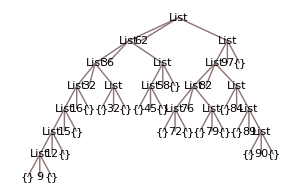

```mathematica
(tree = listToTree[nodes])//TreeForm[#,PlotRangePadding->0,ImageSize->450]&
```

```mathematica
preorder[tree]
```

{62,36,32,16,15,12,9,32,58,45,97,82,76,72,79,84,89,90}

```mathematica
postorder[tree]
```

{9,12,15,16,32,32,45,58,36,72,79,76,90,89,84,82,97,62}

```mathematica
inorder[tree]
```

{9,12,15,16,32,32,36,45,58,62,72,76,79,82,84,89,90,97}

```mathematica
levelorder[tree]
```

{62,36,97,32,58,82,16,32,45,76,84,15,72,79,89,12,90,9}

Discussion

The tree implementation in the solution is a bit simplistic, but it is intended to illustrate basic concepts. One way to generalize the implementation is to allow a different ordering function. It makes sense to keep the ordering with each instance of the tree. For this, it is best to use Mathematica options, which are a standard convention for optional values. You need to redefine the functions for creating trees and accessing their parts, but once you do that, the existing algorithm implementations will still work.

```mathematica
ClearAll[makeTree,getTreeValue,getTreeLeft,getTreeRight,insertTree,listToTree];
(*Use the explicit head Tree to hold the representation and the options.*)
makeTree[opt :OptionsPattern[Ordering -> Less]] :=Tree[{},opt]
makeTree[value_, opt : OptionsPattern[ordering -> Less]] := Tree[{{},value,{}},opt]
(*Functions for extracting the parts of a node are now overloaded for top-level Tree form.*)
getTreeValue[Tree[tree_,___]] := getTreeValue[tree]
getTreeValue[tree_] := tree[[2]]
getTreeLeft[Tree[tree_,___]] := getTreeLeft[tree]
getTreeLeft[tree_] := tree[[1]]
getTreeRight[Tree[tree_,___]] := getTreeRight[tree]
getTreeRight[tree_] := tree[[3]]
(*Insert extracts the ordering option using the replacement rule and passes it to 
 the function that implements the insert.*)
insertTree[Tree[tree_,opts_],value_] := Tree[insertTree[tree,value,ordering /. opts],opts]
insertTree[{},value_,_] := {{},value,{}}
insertTree[tree_, value_,ordering_] := If[ordering[value, getTreeValue[tree]] , 
{insertTree[getTreeLeft[tree],value,ordering],getTreeValue[tree],getTreeRight[tree]},
{getTreeLeft[tree],getTreeValue[tree],insertTree[getTreeRight[tree],value,ordering]}]
listToTree[list_List, opt :OptionsPattern[Ordering -> Less]] := Fold[insertTree[#1, #2] &, makeTree[opt], list]
```

```mathematica
t1 =listToTree[RandomInteger[{1,100}, 20],ordering -> Greater];
inorder[t1]
```

{92,92,91,84,78,71,68,56,56,54,41,39,38,35,34,32,21,16,11,2}

Another enhancement is to generalize the so-called visit function of the traversal  algorithms.

```mathematica
ClearAll[inorder,inorder2];
inorder[tree_,visit_ : Sow ] :=Flatten[ Reap[inorder2[tree,visit]]]
inorder2[{},_] := {} 
inorder2[tree_,visit_] := Module[{},
  inorder2[getTreeLeft[tree],visit];
  visit[getTreeValue[tree]];
  inorder2[getTreeRight[tree],visit]]
```

This allows the caller the option of not receiving all the nodes. For example, rather than Sow, you can pass in a function that writes the values to a file or a filter as we do here.

```mathematica
inorder[t1,If[OddQ[#],Sow[#],#]&]
```

{91,71,41,39,35,21,11}

See Also

More information on trees and tree traversal can be found in any computer science data structures book or at http://bit.ly/7xP6jQ.

ChapterLabel.Heading1  Implementing Ordered Associative Lookup Using a Red-Black Tree

Problem

You need better-than-linear associative lookup and storage to increase performance of a program. You also need the elements to remain ordered.

Solution

A red-black tree is a popular balanced tree algorithm used as the foundation for associative data structures. To implement a red-black tree in Mathematica, you create a representation of the tree and functions for creating, reading, updating, and deleting (CRUD). This implementation will use a head rbTree containing a tree and an ordering relation. The tree is modeled as either an empty list or a quadruple consisting of a color (red or black), a left subtree, an element, and a right subtree. By default, we use the function Less as the ordering relation. Storing the ordering relation as part of the tree allows for trees of varying element content.

```mathematica
(*Make an empty tree with default ordering.*)
makeRBTree[] := rbTree[{},Less]
(*Make an empty tree with a custom ordering.*)
makeRBTree[ordering_] := rbTree[{},ordering]
(*Make a tree with given root and ordering.*)
makeRBTree[{color_,left_,elem_,right_}, ordering_] := rbTree[{color,left,elem,right},ordering]
```

Before we can do much with these trees, we need a method for inserting new elements while keeping the tree well ordered and balanced. For this, we create a top-level insert function implemented in terms of several low-level functions that maintain all the constraints necessary for a red-black tree.

```mathematica
insertRBTree[rbTree[struct_,ordering_], elem_] := makeRBTree[makeBlack[insertRBTree2[struct,elem,ordering]],ordering]
```

```mathematica
(*This implementation method does ordered insertion and balancing of the tree representation. Note: empty subtrees {} are considered implicitly black.*)
insertRBTree2[{},elem_,_] := {red,{},elem,{}}
insertRBTree2[{color_,left_,elem2_,right_},elem1_,ordering_] :=
 Which[ordering[elem1,elem2], balance[color,insertRBTree2[left,elem1,ordering], elem2, right],
            ordering[elem2,elem1], balance[color, left, elem2, insertRBTree2[right,elem1,ordering]],
             True, {color,left,elem2,right}]
```

```mathematica
(*This is a helper that turns a node to black.*)
makeBlack[{color_,left_,elem_, right_}] := {black,left,elem,right}
```

```mathematica
(*Balancing is handled by a transformation function that 
matches all red-black constraint violations and transforms them into balanced versions.*)
balance[black,{red, {red,left1_,elem1_,right1_},elem2_, right2_}, elem3_, right3_] := 
{red,{black,left1,elem1,right1},elem2, {black,right2,elem3,right3}}
balance[black,{red,left1_,elem1_,{red, left2_, elem2_, right1_}},elem3_,right2_] := 
{red, {black, left1, elem1, left2}, elem2, {black,left2,elem3,right2}}
```

```mathematica
balance[black, left1_, elem1_, {red, {red, left2_, elem2_, right1_},elem3_,right2_}] := 
{red, {black, left1, elem1, left2}, elem2, {black, right1,elem3,right2}}
balance[black, left1_, elem1_, {red,left2_,elem2_, {red, left3_, elem3_, right1_}}] := 
{red, {black, left1, elem1, left2}, elem2, {black, left3,elem3,right1}}
balance[color_, left1_,elem1_,right1_] := 
{color, left1,elem1,right1}
```

List-to-tree and tree-to-list conversions are very convenient operations for interfacing with the rest of Mathematica.

```mathematica
(*Given a list create an rbTree of the elements.*)
listToRBTree[list_List] := Fold[insertRBTree[#1, #2] &, makeRBTree[], list]
listToRBTree[list_List,ordering_] := Fold[insertRBTree[#1, #2] &, makeRBTree[ordering], list]
(*Given a tree convert to a list while retaining ordering.*)
rbTreeToList[rbTree[tree_,_]] := Flatten[tree /. (red|black) -> Sequence[],Infinity]
rbTreeFind[rbTree[{},_],_] := {}
rbTreeFind[rbTree[tree_,ordering_], elem_] := rbTreeFind2[tree,elem,ordering]
rbTreeFind2[{color_,left_,elem2_,right_},elem1_,ordering_] := 
Which[ordering[elem1,elem2], rbTreeFind2[left,elem1,ordering],
ordering[elem2,elem1],rbTreeFind2[right,elem1,ordering],
True,{elem2}]
rbTreeMax2[{_,_,elem_,{}}] := elem
rbTreeMax2[{_,_,_,right_}] := rbTreeMax2[right]
removeRBTree[rbTree[{}, ordering_], elem_] := rbTree[{}, ordering]
removeRBTree[rbTree[tree_, ordering_], elem_] := makeRBTree[makeBlack[removeRBTree2[tree, elem, ordering]], ordering]
removeRBTree2[{}, _, _] := {}
```

```mathematica
removeRBTree2[{color_, left_, elem2_, right_}, elem1_, ordering_] :=
   Which[ordering[elem1, elem2], balance[red, removeRBTree2[left, elem1, ordering], elem2, right],
                ordering[elem2, elem1], balance[red, left, elem2, removeRBTree2[right, elem1, ordering]],
                 True, Which[right == {}, left,
   				left == {}, right,
   				True, With[{max = rbTreeMax2[left]}, balance[red, removeRBTree2[left, max, ordering], max, right]]]
  ]
```

Discussion

There are several ways to approach a problem like this. One reasonable answer is to implement associative lookup outside of Mathematica using a language like C++ and then use MathLink to access this functionality. Here we will take the approach of implementing a red-black tree directly in Mathematica.

A red-black tree implemented in C may typically be hundreds of lines of code, yet we achieve an implementation in Mathematica with less than a hundred, including comments. How is this possible? The main idea is to exploit pattern matching as much as possible. Note particularly the function balance. This function directly implements the most tricky part of a red-black-tree implementation in a traditionally procedural language by stating the balancing rules in a form that is very close to the way the algorithm requirements might specify them. Let’s take one of the versions as an example.

```mathematica
balance[black, {red, {red, left1_, elem1_, right1_}, elem2_, right2_}, elem3_, right3_] := 
 {red, {black, left1, elem1, right1}, elem2, {black, right2, elem3, right3}}
```

The above says: “If you find a black node (elem3) with a red left child (elem2) that also has a red left child (elem1), then convert to a red node with two black children (elem1 and elem3, in that order). This is a case where the code speaks more clearly and precisely than any English translation. With a slight bit of editing, the code itself translates into a graphical view of before and after. I can’t think of another general programming language where you can code and visualize an algorithm with so little added effort!

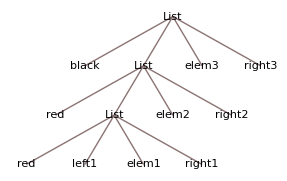

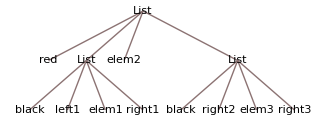

```mathematica
TreeForm[{black, {red, {red, left1, elem1, right1}, elem2, right2}, elem3, right3} ,ImageSize->Medium]
TreeForm[{red, {black, left1, elem1, right1}, elem2, {black, right2, elem3, right3}},ImageSize->450]
```

See Also

A solution to associative lookup that is more in the spirit of Mathematica can be found in Recipe 3.13.

This recipe was inspired by the book Purely Functional Data Structures by Chris Okasaki (Cambridge University Press), in which Haskell is used to demonstrate that data structures can be written under the constraints of a pure functional programming language.

Wikipedia provides a good basic explanation of and references to more sources for red-black trees (http://bit.ly/3WEqrT).

ChapterLabel.Heading1  Exploiting Mathematica’s Built-In Associative Lookup

Problem

You want to create a dictionary to associate keys with values, but you want Mathematica to do most of the work.

Solution

Harness the same mechanism Mathematica uses to locate the downvalues of a symbol to create the dictionary.

Here I outline the basic idea for the solution and defer the actual implementation to the discussion. The idea is simply to exploit something that Mathematica must already do well: look up a symbol’s downvalues. It must do this well because it is central to Mathematica programming. Imagine you want to create a table of values associating some U.S. zip codes with towns. A reasonable way to proceed is as follows:

```mathematica
zipcode[11771] = {"Oyster Bay", "Upper Brookville", "East Norwhich", "Cove Neck", "Centere Island"};
zipcode[11772] = {"Patchogue","North Patchogue", "East Patchogue"};
(*And so on...*)
zipcode[11779] = {"Ronkonkoma","Lake Ronkonkoma"};
```

Now, when your program needs to do a lookup, it can simply call the “function” zipcode.

```mathematica
With[{zip=11771},
Print["The number of towns in ",zip, " is ", Length[zipcode[zip]], ";"];]
```

The number of towns in 11771 is 5.

This is so obvious that few regular Mathematica programmers would even think twice about doing this. However, this use case is static. Most associative data structures are dynamic. This is not a problem because you can also remove downvalues.

```mathematica
zipcode[11779] =.
```

Now there is no longer an association to 11779. Mathematica indicates this by returning the expression in unevaluated form.

```mathematica
zipcode[11779]
```

zipcode[11779]

But this is still not enough. An associated data structure should also tell you all the keys and all the values it knows. Again, Mathematica comes through.

```mathematica
DownValues[zipcode]
```

{HoldPattern[zipcode[11771]]:>{Oyster Bay,Upper Brookville,East Norwhich,Cove Neck,Centere Island},HoldPattern[zipcode[11772]]:>{Patchogue,North Patchogue,East Patchogue}}

So all the building blocks are present in the core of Mathematica to create a dynamic dictionary-like data structure. All that is needed is the creation of some code to neatly tie these pieces together into a general utility.

Discussion

The first function we need is a way to construct a dictionary. In the solution, we use a symbol that makes sense for the problem at hand, but in a generic implementation what symbol is used is not significant so long as it is unique. Luckily, Mathematica has the function Unique to deliver the goods. We initialize the dictionary by creating a downvalue that maps any value to the empty list. The symbol is wrapped up in the head Dictionary and returned to the caller.

```mathematica
makeDictionary[] := 
 	Module[{name},
  		name = Unique["dict"] ;
  		Evaluate[name][k_] := {};
  		Dictionary[name]
  	]
```

You will also want a way to get rid of dictionaries and all their content. Remove does the trick.

```mathematica
destroyDictionary[Dictionary[name_,___]]:=If[ValueQ[name[_]],Remove[name];True,False]
```

Although we said that there is no need to know the symbol used internally, there is no harm in providing a function to retrieve it. Further, our implementation will use this function so that it is easier to change the internal representation in the future.

```mathematica
dictName[Dictionary[name_,___]]:=name
```

The most important function, dictStore, allows the association of a value with a key. We assume, as in the solution, that more than one value may be needed for a given key, so we store values in a list and prepend new values as they are added.

```mathematica
dictStore[dict_Dictionary,key_,value_]:=Module[{d=dictName[dict]},d[key]=Prepend[d[key],value]]
```

The function dictReplace is like dictStore, except it guarantees value is unique. That is, there are no duplicates of value, although there might be other values for the key.

```mathematica
dictReplace[dict_Dictionary,key_,value_]:=Module[{d=dictName[dict]},d[key]=d[key]∪{value}]
```

In contrast, the function dictRemove ensures that there are no instances of value  associated with the key (although, again, there might be other values for the key).

```mathematica
dictRemove[dict_Dictionary,key_,value_]:=Module[{d=dictName[dict]},d[key]=Complement[d[key],{value}]]
```

If you want all values removed, then use dictClear.

```mathematica
dictClear[Dictionary[name_,___]]:=If[ValueQ[name[_]],Clear[name];Evaluate[name][k_]:={};True,False]
```

Maintaining the dictionary is all well and good, but you also need to be able to retrieve values. The function dictLookup is the easiest to implement because it gets Mathematica to do all the work by simply asking for the downvalue in the usual way.

```mathematica
dictLookup[Dictionary[name_,___],key_]:=name[key]
```

Sometimes you might not care what the value is but rather if the key exists at all. Here I use ValueQ, which returns true if the evaluation of an expression returns something different than the expression itself (hence, indicating there is a value). In this implementation, I don’t care that the value may be the empty list {} because dictHasKeyQ is only intended to tell the caller that the key is present.

```mathematica
dictHasKeyQ[Dictionary[name_,___],key_]:=ValueQ[name[key]]
```

This function tells you that the key is present but has no values.

```mathematica
dictKeyEmptyQ[Dictionary[name_,___],key_]:= name[key] === {}
```

In some applications, you may want to know the set of all keys; dictKeys provides that. It works by using DownValues, as shown in the solution, but transforms the results to extract only the keys. Most is used to exclude the special downvalue name[k_], which was created within makeDictionary. The use of HoldPattern follows from the format that DownValues uses, as seen in the solution section. Here, Evaluate is used because DownValues has the attribute HoldAll.

```mathematica
dictKeys[dict_Dictionary]:=Most[DownValues[Evaluate[dictName[dict]]]]/.HoldPattern[a_:>_List]:>a⟦1,1⟧
```

Another useful capability is to get a list of all key value pairs; dictKeyValuePairs does that.

```mathematica
dictKeyValuePairs[dict_Dictionary]:=Most[DownValues[Evaluate[dictName[dict]]]]/.HoldPattern[a_:>values_List]:>{a⟦1,1⟧,values}
```

Before I exercise this functionality, a few general points need to be made.

You may be curious about the pattern Dictionary[name_, ___] since the representation of the dictionary, per makeDictionary, is clearly just Dictionary[name]. As you probably already know (see Chapter 4 if necessary), ___ matches a sequence of zero or more expressions. Using this pattern will future proof the functions against changes in the implementation. For example, I may want to enhance Dictionary to take options that control aspects of its behavior (for example, whether duplicate values are allowed for a key or whether a key can have multiple values all together). Keep this in mind when creating your own data structures.

A collection of functions like this really begs to be organized more formally as a Mathematica package. In fact, you can download such a package, with the source code, at this book’s website, http://oreilly.com/catalog/9780596520991/. I cover packages in Recipe 18.4.

Here is how I might code the zip codes example from the solution if I needed the full set of create, read, update, and delete capabilities that Dictionary provides.

```mathematica
zipcodes = makeDictionary[];
dictStore[zipcodes,11771,#]& /@   {"Oyster Bay", "Upper Brookville", "East Norwhich", "Cove Neck", "Centere Island"};
dictStore[zipcodes,11772,#]& /@   {"Patchogue","North Patchogue", "East Patchogue"};
dictStore[zipcodes,11779,#]& /@    {"Ronkonkoma","Lake Ronkonkoma"};
```

```mathematica
dictLookup[zipcodes,11771]
```

{Centere Island,Cove Neck,East Norwhich,Upper Brookville,Oyster Bay}

```mathematica
dictLookup[zipcodes,99999]
```

{}

Ask if a key is present.

```mathematica
dictHasKeyQ[zipcodes,11779]
```

True

Get all the zip codes stored.

```mathematica
dictKeys[zipcodes]
```

{11771,11772,11779}

In Recipe 3.12, “Red-Black Trees,” quite a bit more coding is required to get a similar level of functionality. This recipe is relatively easy because it leverages one of Mathematica’s strengths. This is an important lesson when working with Mathematica (or any language). Always look for solutions that play to the language’s strengths rather than using hack solutions designed for other programming environments. To be fair, the red-black-tree implementation has features that would be more difficult to support in this recipe. Specifically, we could control the ordering of keys with red-black tree, but here keys are ordered according to Mathematica’s conventions (which are conveniently in line with the expectations one would have for a dictionary).

ChapterLabel.Heading1  Constructing Graphs Using the Combinatorica` Package

Problem

You are solving a problem modeled as a graph and need to create that graph for use with Combinatorica` package’s algorithms.

Solution

If your graph is almost complete, construct a complete graph and remove unwanted edges.

```mathematica
Needs["Combinatorica`"]
```

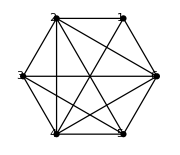

```mathematica
g1 = CompleteGraph[6];
g1 = DeleteEdges[g1, {{1,5},{1,3}}];
ShowGraph[g1,VertexNumber->True,ImageSize->Small]
```

If your graph is sparse, construct directly.

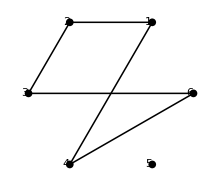

```mathematica
ShowGraph[FromUnorderedPairs[{{1,2},{1,4},{2,3},{3,6},{4,6}}] ,VertexNumber->True,ImageSize->Small]
```

Use MakeGraph if your graph can be defined by a predicate.

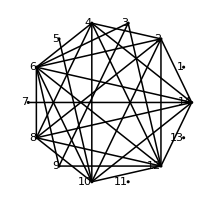

```mathematica
ShowGraph[MakeGraph[Range[14],!CoprimeQ[#1,#2]&&#1 ≠ #2&,Type->Undirected],VertexNumber->True,VertexStyle->Directive[PointSize[0.01]],ImageSize->Small]
```

Discussion

Graphs can also be constructed from combinations of existing graphs by using GraphUnion, GraphIntersection, GraphDifference, GraphProduct, and GraphJoin. In the examples given here, I always use two graphs, but the operations are generalized to multiple graphs.

GraphUnion always creates a disjoint graph resulting from the combination of the graphs in the union.

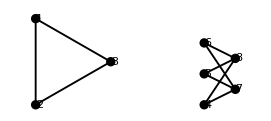

```mathematica
ShowGraph[GraphUnion[CompleteGraph[3],CompleteGraph[3,2]],VertexLabel->True]
```

GraphJoin performs a union and then links up all the vertices from the corresponding graphs.

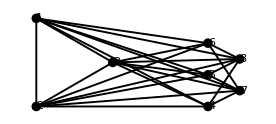

```mathematica
ShowGraph[GraphJoin[CompleteGraph[3],CompleteGraph[3,2]],VertexLabel->True]
```

GraphIntersection works only on graphs with the same number of vertices and  produces a graph where the input graphs have edges in common.

```mathematica
g1 =DeleteEdge[CompleteGraph[5],{1,2}];
 g2 =DeleteEdge[CompleteGraph[5],{2,3}];
 ShowGraphArray[{g1,g2,GraphIntersection[g1,g2]},VertexLabel->True]
```

-Graphics-

GraphDifference creates a graph with all the edges that are in the first graph but not in the second.

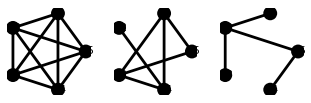

```mathematica
g1 =CompleteGraph[5];
 
g2 =DeleteEdges[CompleteGraph[5],{{1,2},{2,3},{2,5},{4,5}}];
 ShowGraphArray[{g1,g2,GraphDifference[g1,g2]},VertexLabel->True]
```

GraphProduct creates a graph by injecting copies of the first graph into the second at each vertex of the second and then connecting the vertices of the injected graphs.

Unlike a numerical product, this operation is not commutative, as demonstrated in Out[354] on page 138.

```mathematica
g1= CompleteGraph[3];
g2 =CompleteGraph[3,2];
ShowGraphArray[{{g1,g2},{GraphProduct[g1,g2],GraphProduct[g2,g1]}},VertexLabel->True,ImageSize->Medium]
```

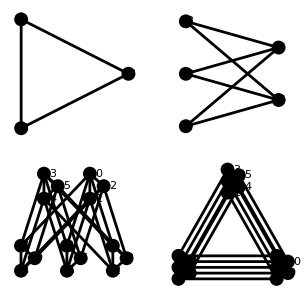

Another way to construct graphs is from alternate representations, such as adjacency matrices and adjacency lists. Out[355] on page 139 shows a graph constructed from an adjacency matrix obtained from GraphData. Normal is used to convert SparseMatrix, since Combinatorica does not recognize sparse-matrix representations.

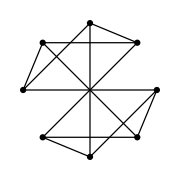

```mathematica
ShowGraph[FromAdjacencyMatrix[Normal[GraphData["CubicalGraph","AdjacencyMatrix"]]],ImageSize-> Small]
```

Combinatorica also supports directed graphs and graphs with weighted edges. Using SetEdgeWeights alone gives random real weights in the range [0,1]. SetEdgeWeights also accepts WeightingFunction and WeightRange options. You can also explicitly specify the weights in a list, which will be assigned to the edges in the same order as returned by the function Edges.

```mathematica
SeedRandom[1];
g1=RandomGraph[5,0.3,Type->Directed];
g1=SetEdgeWeights[g1,WeightingFunction->RandomInteger,WeightRange->{1,10}];
g2 = MakeUndirected[g1];
(*The number of weights must match the number of edges or you'll get garbage!*)
g2 = SetEdgeWeights[g2,{1,2,3,4,5,6,7}];
SetGraphOptions[g2,Type->Directed];
GraphicsRow[{ShowGraph[SetEdgeLabels[g1,GetEdgeWeights[g1]],ImagePadding->{{40,0},{0,0}}],ShowGraph[SetEdgeLabels[g2,GetEdgeWeights[g2]],ImagePadding->{{40,0},{0,0}}]},BaseStyle->{FontSize->10},ImageSize->Medium]
```

See Also

The definitive reference to Combinatorica is Computational Discrete Mathematics: Combinatorics and Graph Theory with Mathematica by Sriram Pemmaraju and Steven Skiena (Cambridge University Press). This reference is essential if you intend to use Combinatorica in a serious way, because the documentation that comes bundled with Mathematica is very sparse.

Mathematica has an alternate graph package called GraphUtilities` that represents graphs using lists of rules (e.g., {a→b, a→c, b→c}). There is a conversion function to Combinatorica` graphs. Search for GraphUtilities in the Mathematica documentation.

ChapterLabel.Heading1  Using Graph Algorithms to Extract Information from Graphs

Problem

You want to test a graph for specific properties or find paths through a graph with specific properties or which satisfy specific constraints.

Solution

There are many graph theoretic functions in the Combinatorica` package related to shortest paths, network flows, connectivity, planarity testing, topological sorting, and so on. The solutions and following discussion show a sampling of some of the more popular graph algorithms.

Out[363]a shows a graph generated from a complete graph with select edges removed. The graph in Out[363]b is the minimum spanning tree of Out[363]a, and Out[363]c is the shortest path spanning tree.

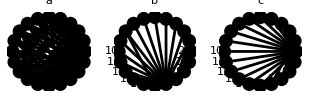

```mathematica
Module[{g,edges},
(*Start with a complete graph.*)
g=CompleteGraph[20];
(*Generate some edges to remove.*)
{dummy,{edges}} = Reap[Do[If[Mod[j,i]<7 , Sow[{i,j}],Null],{i,1,20},{j,i+1,15}]];
(g =DeleteEdge[g,#])& /@ edges;
(*Weight the edges randomly.*)
SeedRandom[1]; (*Make random edge weights repeatable.*)
SetEdgeWeights[g];
(*Demonstrate MinimumSpanningTree and ShortestPathSpanningTree.*)
GraphicsRow[{ShowGraph[g,PlotLabel->"a"],ShowGraph[MinimumSpanningTree[g],VertexNumber->True,PlotLabel->"b"],ShowGraph[ShortestPathSpanningTree[g,1],VertexNumber->True,PlotLabel->"c"]},ImageSize->450]
]
```

Discussion

Properties of graphs can be tested using a variety of functions, such as HamiltonianQ (which has a cycle that visits each vertex once), EulerianQ (which has a tour that traverses each edge once), AntisymmetricQ, ReflexiveQ, UndirectedQ, SelfLoopsQ, and so on. There are over 40 such predicates in Combinatorica.

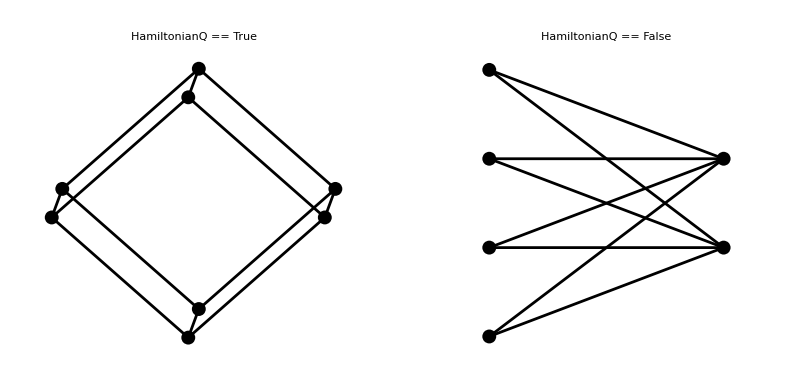

```mathematica
g1 =Hypercube[3];g2=CompleteGraph[4,2];
GraphicsRow[{ShowGraph[g1,PlotLabel->"HamiltonianQ == " <> ToString[HamiltonianQ[g1]]],
ShowGraph[g2,PlotLabel->"HamiltonianQ == " <> ToString[HamiltonianQ[g2]]]}]
```

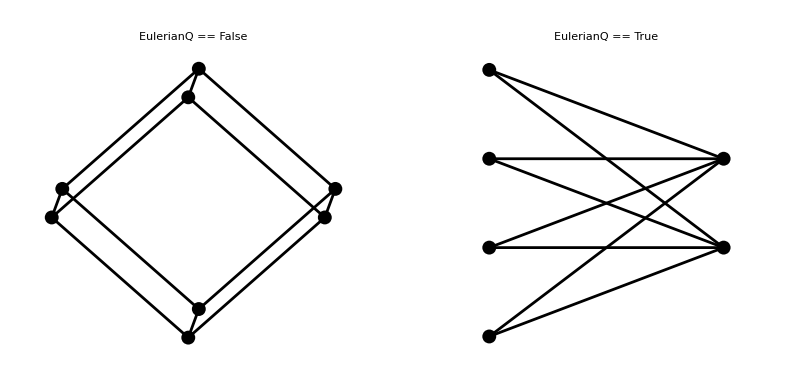

```mathematica
GraphicsRow[{ShowGraph[g1,PlotLabel->"EulerianQ == " <> ToString[EulerianQ[g1]]],
ShowGraph[g2,PlotLabel->"EulerianQ == " <> ToString[EulerianQ[g2]]]}]
```

A directed graph with no cycles is called a directed acyclic graph (DAG). The transitive closer of a DAG is the supergraph that adds directed edges from ancestors to descendants.

```mathematica
g =CompleteBinaryTree[7];
e = Reverse[Edges[g],{2}];
g = DeleteEdges[MakeDirected[g],e];
{AcyclicQ[g],TopologicalSort[TransitiveClosure[g]]}
```

{True,{1,2,3,4,5,6,7}}

Out[371] shows the tree and its transitive closure. When you display highly connected graphs (like the transitive closure) with vertex labels, it often helps to use opacity or font control to make sure vertex labels are not obscured by the edges.

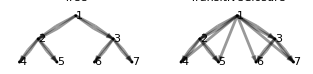

```mathematica
Module[{opts},
opts= Sequence[VertexLabel->True,BaseStyle->{FontWeight->Bold,FontSize->12},LabelStyle->{FontWeight->Medium},
VertexStyle->Disk[0.005],EdgeStyle->Opacity[0.4]];
GraphicsRow[{ShowGraph[g,opts,PlotLabel->"Tree"],ShowGraph[TransitiveClosure[g],opts,PlotLabel->"TransitiveClosure"]},ImageSize->450]]
```

See Also

See Chapters 7 and 8 in Computational Discrete Mathematics: Combinatorics and Graph Theory with Mathematica by Sriram Pemmaraju and Steven Skiena.